## 3.029 Spring 2022 Lecture 17 - 04/04/2022

## Surface Tension & Energy

This week, we will develop the thermodynamics of interfaces in crystalline materials

In particular, we’ll investigate the surface tension terms arising from finite size particles using the Lennard-Jones potential

As well as the orientational-dependent of surface energy

Next lecture, we’ll investigate the implications of this orientational dependence on the equilibrium shapes of crystals using the Wulff construction

## Surface Tension in Lennard-Jones Particles

### Finite-Size Particles

Recall the normalized Lennard-Jones potential for a pair of atoms a distance ρ=r/r_min apart is given by:

```mathematica
lennardJonesPotentialNonDimensional[ρ_]=1/ρ^12-2/ρ^6;
```

The sum of pairwise energies each atom in a particle experiences is similarly given by:

Note, we are dividing by two to avoid double-counting, and the 1/2 term is to account for the additional self-energy terms we introduced by setting the diagonal to ρ=1

```mathematica
lennardJonesEnergies[pts_?MatrixQ]:= Block[
{
distanceMatSquared =DistanceMatrix[pts, DistanceFunction->SquaredEuclideanDistance] + IdentityMatrix[Length[pts]],
distanceMatSixth
},
distanceMatSixth= distanceMatSquared^3;
1/2+1/2 Total[1/distanceMatSixth^2 - 2/distanceMatSixth]
]
```

As we saw in L13, non-hexagonal lattices undergo a lattice instability when interacting with pairwise central potentials in 2D

As such, we’ll focus on hexagonal particles

We first make a list of hexagonal lattice sites from which we can “punch-out” round particles of a specified radius

We need to ensure it’s large enough for the largest particle we’d like to punch out, say 50 normalized units

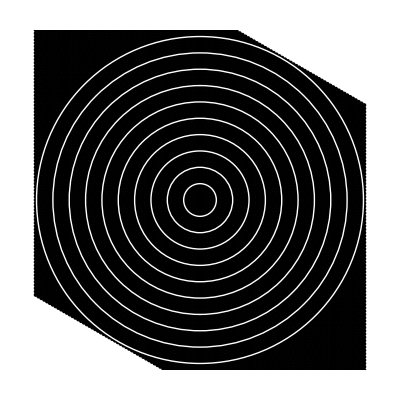

```mathematica
hexagonalLatticeVectors = {{0,1},{-(√3)/2,1/2}};
hexagonalLatticePoints=With[{range=Ceiling[50/((√3)/2)]},N[Tuples[Range[-range,range],2].hexagonalLatticeVectors]];
Graphics[{Point[hexagonalLatticePoints],White,Thick,Circle[{0,0},#]&/@Range[5,50,5]},PlotRange->50{{-1,1},{-1,1}},PlotRangePadding->1]
```

And write a simple “punch” function

```mathematica
hexagonalParticle[radius_,latticePoints_:hexagonalLatticePoints]:=hexagonalParticle[radius,latticePoints]= Select[Norm[#]<radius&][latticePoints]
```

To see the effect of surface tension, let’s color each particle by its energy

```mathematica
energyColor[{eMin_,eMax_},power_:0.25,cf_:ColorData["DarkRainbow"]][energy_]:= cf[
(Rescale[Clip[energy,{eMin,eMax}],{eMin,eMax},{0,1}])^power]

particleGraphic[{eMin_,eMax_},power_:0.25,cf_:ColorData["DarkRainbow"]][positions_]:= MapThread[{energyColor[{eMin,eMax},power,cf][#1],Disk[#2,1/2]}&,{lennardJonesEnergies[positions],positions}]
```

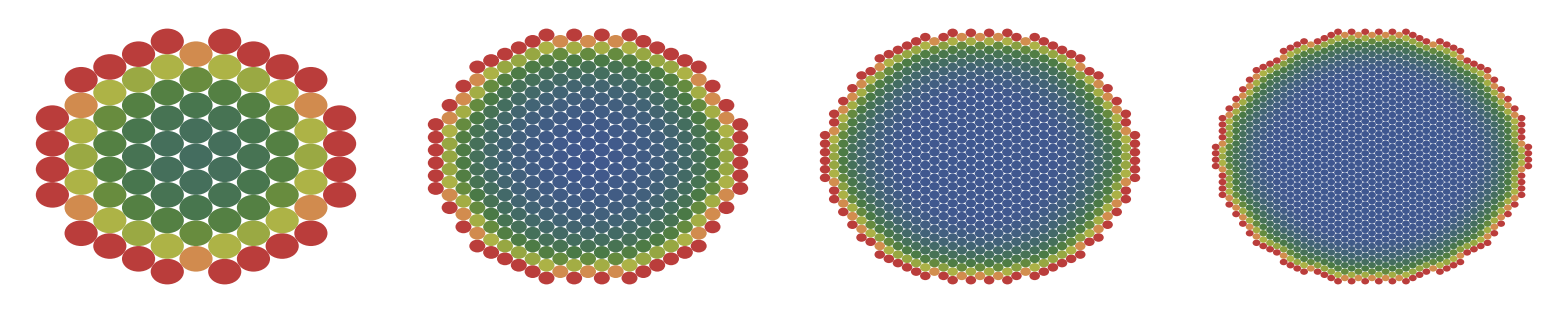

```mathematica
{ljEnergyMinimum,ljEnergyMaximum}=MinMax[lennardJonesEnergies[hexagonalParticle[50]]];
Multicolumn[Graphics@*particleGraphic[{ljEnergyMinimum,ljEnergyMaximum}]@*hexagonalParticle/@{5,10,15,20},4]
```

Notice we used a sub-linear power law in our color function (n=0.25)

This is to give more contrast to the lower parts of the energy distribution and increase the “diffuse” width of the surface

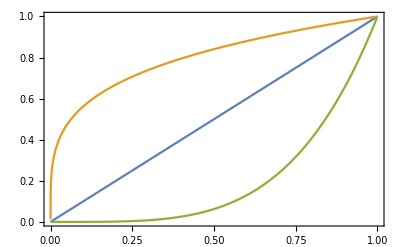

```mathematica
Plot[{x,x^0.25,x^4},{x,0,1},Frame->True]
```

As we’ve seen before, atoms on the surface have a higher average energy

### Excess Average Surface Energy

We’ll use these particles to estimate the excess energy due to the presence of a surface

The idea is to try and make increasingly larger and larger particles and compute the average energy per particle

As the particle becomes larger, the fraction of particles on the surface becomes smaller, and thus contributing less to the average energy

```mathematica
particles = <|# -> hexagonalParticle[#]&/@Range[5,50] |>;
```

```mathematica
aggregatedLennardJonesEnergies[positions_]:=aggregatedLennardJonesEnergies[positions]=With[{es=lennardJonesEnergies[positions]},<|"Energies"->es,"Total Energy"->Total[es],"Average Energy"->Mean[es]|>]
```

The magnitude of the total energy naturally increases with particle radius

Remember, the potential is normalized to have a value of -1 at a normalized distance of ρ=1

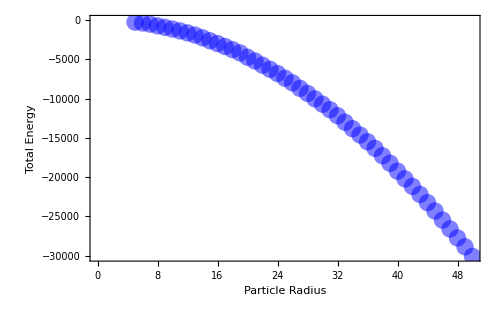

```mathematica
With[{totalEnergies=(aggregatedLennardJonesEnergies/@particles)[[All,"Total Energy"]]},
ListPlot[totalEnergies,Frame->True,FrameLabel->{"Particle Radius","Total Energy"},LabelStyle->Directive[Black,16],ImageSize->500,PlotStyle->Directive[PointSize[0.025],Opacity[0.5],Blue]]
]
```

Without a surface, we would expect the total energy to decrease linearly with the number of particles

Let’s plot this as an average energy per particle to see this better

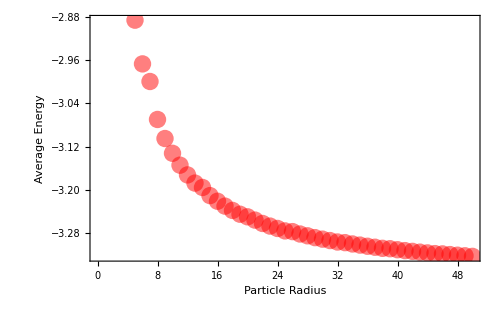

```mathematica
With[{averageEnergies=(aggregatedLennardJonesEnergies/@particles)[[All,"Average Energy"]]},
ListPlot[averageEnergies,Frame->True,FrameLabel->{"Particle Radius","Average Energy"},LabelStyle->Directive[Black,16],ImageSize->500,PlotStyle->Directive[PointSize[0.025],Opacity[0.5],Red]]
]
```

We’ll use this data to fit a power-law model, to extrapolate the average energy as the particle size goes to infinity

```mathematica
averageEnergyModel=constantValue + sizeDependentValue /radius^power;
averageEnergyModelFit=With[{averageEnergies=(aggregatedLennardJonesEnergies/@particles)[[All,"Average Energy"]]},
FindFit[KeyValueMap[List,averageEnergies],averageEnergyModel,{constantValue,sizeDependentValue,power},radius]
]
```

{constantValue→-3.36986,sizeDependentValue→2.53214,power→1.02108}

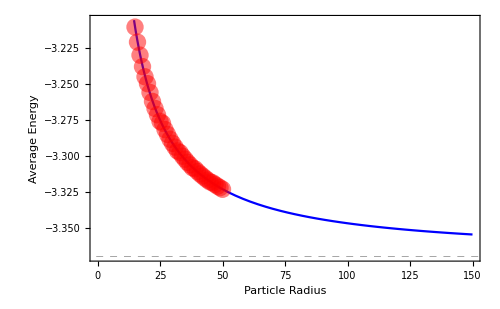

```mathematica
With[{averageEnergies=(aggregatedLennardJonesEnergies/@particles)[[All,"Average Energy"]],min=constantValue/.averageEnergyModelFit},
Show[Plot[averageEnergyModel/.averageEnergyModelFit,{radius,5,150},Frame->True,FrameLabel->{"Particle Radius","Average Energy"},LabelStyle->Directive[Black,16],PlotRangePadding->{Automatic,Scaled[.05]},PlotRange->{min,Automatic},ImageSize->500,PlotStyle->Blue,GridLinesStyle->Directive[Gray, Dashed],GridLines->{None,{min}}],ListPlot[averageEnergies,PlotStyle->Directive[PointSize[0.025],Opacity[0.5],Red]]
]]
```

The excess energy per atom goes like

### Excess Total Surface Energy

This is related to the Gibbs-Thomson effect

And we can relate this to the curvature of our particle by looking at the rate of surface energy increase with respect to volume

Note: since we’re in 2D, “volume” here refers to the particle’s area, and “area” refers to the circumference

```mathematica
With[{
volume=π r^2,
area = 2π r
},
D[area ,r]/D[volume,r]
]
```

1/r

In-fact, let’s use this form to provide another estimate for the surface tension based on the total energy

```mathematica
totalEnergyModel=bulkEnergy (Pi radius^2) + γ (2 Pi radius);
totalEnergyModelFit=With[{totalEnergies=(aggregatedLennardJonesEnergies/@particles)[[All,"Total Energy"]]},
FindFit[KeyValueMap[List,totalEnergies],totalEnergyModel,{bulkEnergy,γ},radius]
]
```

{bulkEnergy→-3.9007,γ→1.6842}

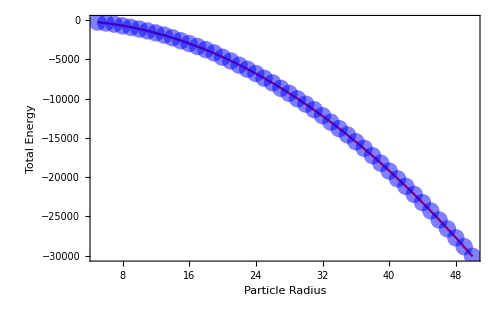

```mathematica
With[{totalEnergies=(aggregatedLennardJonesEnergies/@particles)[[All,"Total Energy"]]},
Show[Plot[totalEnergyModel/.totalEnergyModelFit,{radius,5,50},Frame->True,FrameLabel->{"Particle Radius","Total Energy"},LabelStyle->Directive[Black,16],ImageSize->500,PlotStyle->Red],ListPlot[totalEnergies,PlotStyle->Directive[PointSize[0.025],Opacity[0.5],Blue]]
]]
```

Looking at our two fits we notice a curious discrepancy in the constant (surface-independent) terms

```mathematica
totalEnergyModelFit
```

{bulkEnergy→-3.9007,γ→1.6842}

```mathematica
averageEnergyModelFit
```

{constantValue→-3.36986,sizeDependentValue→2.53214,power→1.02108}

```mathematica
(constantValue/.averageEnergyModelFit)/(bulkEnergy/.totalEnergyModelFit)
```

0.863912

The discrepancy is resolved by noting that the bulk energy fit is per unit-area, while the average energy fit is per atom

Each atom in our hexagonal lattice takes up √3/2 normalized units of area

We can see this directly from the Determinant of the hexagonal lattice vectors

```mathematica
Det[hexagonalLatticeVectors]
```

(√3)/2

As well as more visually/numerically using a Voronoi Mesh

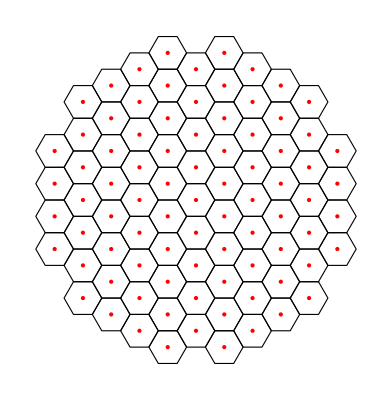

0.866025

```mathematica
Block[{voronoi=VoronoiMesh[hexagonalParticle[6]],interior,pts=Select[hexagonalParticle[6],Norm[#]<5&]},
interior=MeshPrimitives[voronoi,{2,"Interior"}];
interior=Select[interior,Norm[RegionCentroid[#]]<5&];
Echo[Graphics[{
{EdgeForm[Black],FaceForm[None],interior},
{Red,PointSize[Large],Point[pts]}
}]];
Mean[RegionMeasure/@interior]
]
```

## Thermodynamics of Surfaces

Notice we used the symbol γ above for the surface-energy dependent term we multiplied by the surface’s “area”

This γ term is called the surface-energy and we quickly summarize its canonical thermodynamic treatment, following Gibbs

To do so, we need to introduce the concept of Gibbs dividing surface, which is most conveniently demonstrated by considering an interface between a bicrystal

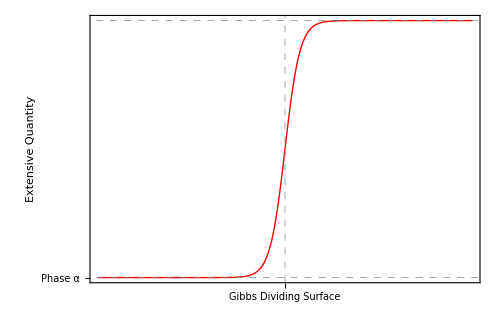

```mathematica
Plot[LogisticSigmoid[x],{x,-25,25},Frame->True,Axes->False,GridLines->{{0},{0,1}},GridLinesStyle->Directive[Gray, Dashed],PlotStyle->{Red,Thick},ImageSize->500,LabelStyle->Directive[Black,16],FrameTicks->{{{{0,"Phase α"}},{{1,"Phase β"}}},{{{0,"Gibbs Dividing Surface"}},None}},FrameLabel->{None,"Extensive Quantity"}]
```

In general, interfaces between various thermodynamic phases are “diffuse”

i.e. there is a transition region separating the two phases (defined using their extensive quantities above)

To avoid the complications arising from this diffuseness, Gibbs defined a mathematical plane with area A, known as the dividing surface

This allowed him to define interfacial extensive quantities by subtracting from the extensive quantity of the system containing the interface a hypothetical reference system consisting of two bulk phases, extending uniformly up to the dividing surface

Recall that the variation of the internal energy of bulk phase α with respect to its extensive variables is given by

and similarly for phase β:

For the system containing the interface we can similarly write

where we note that the interface has no volume, but instead introduces a surface energy term multiplied by the change in area dA

Since the two phases are at equilibrium, we note that , and accumulate the other extensive variables are

Finally, since all the differentials above are extensive, we can integrate the expression to give

## Surface Reconstructions

### Uniform Strain Relaxation

All of the calculations above assumed a particle lattice constant at ρ=1

This was the normalized equilibrium lattice constant for a pair of atoms

However, the long-range attractive force of the potential suggests that the particle will experience non-negligible second- and third-nearest neighbor interactions too

This will cause the lattice constant to be slightly different

As a first pass, we can try and find this new lattice constant for uniform strain

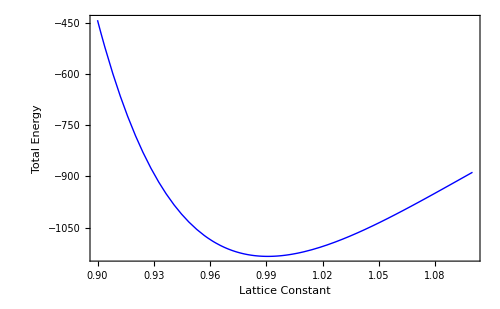

```mathematica
With[{positions = hexagonalParticle[10]},
Plot[
aggregatedLennardJonesEnergies[newLatticeConstant positions]["Total Energy"],
{newLatticeConstant,0.9,1.1},
Frame->True,FrameLabel->{"Lattice Constant","Total Energy"},ImageSize->500,LabelStyle->Directive[Black,16],PlotStyle->Directive[Thick,Blue]
]
]
```

We can see visually that the minimum is slightly less than 1

Let’s investigate the total energy for small particles symbolically

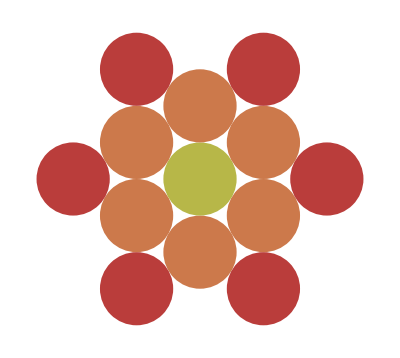

```mathematica
Graphics[particleGraphic[{ljEnergyMinimum,ljEnergyMaximum}][hexagonalParticle[2]]]
```

```mathematica
With[{positions=hexagonalParticle[2]},
Apart[FullSimplify[
aggregatedLennardJonesEnergies[newLatticeConstant positions]["Total Energy"],newLatticeConstant>0]]
]
```

24.0285/newLatticeConstant^12-49.892/newLatticeConstant^6

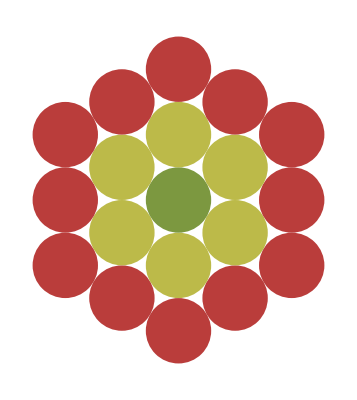

```mathematica
Graphics[particleGraphic[{ljEnergyMinimum,ljEnergyMaximum}][hexagonalParticle[2.5]]]
```

```mathematica
With[{positions=hexagonalParticle[2.5]},
Apart[FullSimplify[
aggregatedLennardJonesEnergies[newLatticeConstant positions]["Total Energy"],newLatticeConstant>0]]
]
```

42.0481/newLatticeConstant^12-87.3316/newLatticeConstant^6

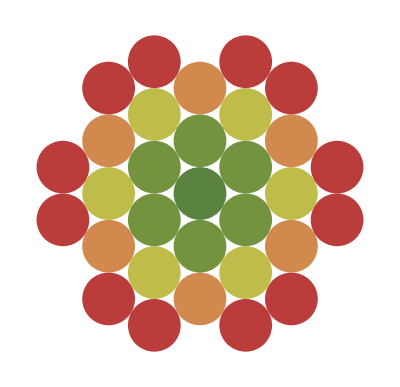

```mathematica
Graphics[particleGraphic[{ljEnergyMinimum,ljEnergyMaximum}][hexagonalParticle[3]]]
```

```mathematica
With[{positions=hexagonalParticle[3]},
Apart[FullSimplify[
aggregatedLennardJonesEnergies[newLatticeConstant positions]["Total Energy"],newLatticeConstant>0]]
]
```

72.0956/newLatticeConstant^12-150.726/newLatticeConstant^6

This suggests we can minimize the total energy symbolically as:

```mathematica
symbolicTotalEnergy[newLatticeConstant_] = twelfthPowerCoefficient/newLatticeConstant^12  -2 sixthPowerCoefficient/newLatticeConstant^6;
First[SolveValues[symbolicTotalEnergy'[newLatticeConstant]==0,newLatticeConstant]]
```

-twelfthPowerCoefficient^(1/6)/sixthPowerCoefficient^(1/6)

We can extract the coefficients using a very similar function as our total energy function

```mathematica
minimizingLatticeConstant[pts_]:=
Block[{
distanceMatSquared =DistanceMatrix[pts, DistanceFunction->SquaredEuclideanDistance] + IdentityMatrix[Length[pts]],
twelfthPowerCoefficient,sixthPowerCoefficient
},
twelfthPowerCoefficient=  Total[1/distanceMatSquared^6,2]-Length[pts];
sixthPowerCoefficient=Total[1/distanceMatSquared^3,2]-Length[pts] ;
(twelfthPowerCoefficient/sixthPowerCoefficient)^(1/6)

]
```

```mathematica
latticeConstantData=minimizingLatticeConstant/@particles
```

<|5→0.991639,6→0.991403,7→0.991121,8→0.990995,9→0.990912,10→0.990846,11→0.990792,12→0.990747,13→0.990708,14→0.990652,15→0.990617,16→0.990593,17→0.990572,18→0.990553,19→0.990536,20→0.990509,21→0.990496,22→0.990481,23→0.99047,24→0.99046,25→0.990449,26→0.990435,27→0.990427,28→0.990419,29→0.990411,30→0.990405,31→0.990399,32→0.990393,33→0.990384,34→0.990379,35→0.990374,36→0.990369,37→0.990365,38→0.990361,39→0.990355,40→0.99035,41→0.990347,42→0.990344,43→0.99034,44→0.990337,45→0.990334,46→0.99033,47→0.990327,48→0.990324,49→0.990322,50→0.99032|>

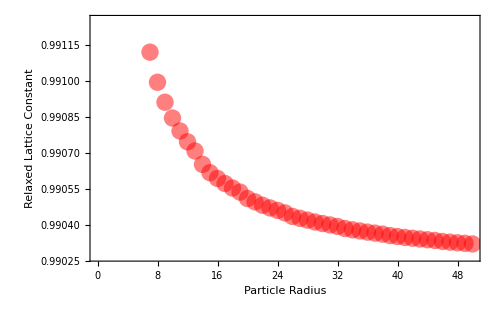

```mathematica
ListPlot[latticeConstantData,Frame->True,FrameLabel->{"Particle Radius","Relaxed Lattice Constant"},LabelStyle->Directive[Black,16],ImageSize->500,PlotStyle->Directive[PointSize[0.025],Opacity[0.5],Red]]
```

The plot above motivates us to use a statistical approach to fit a functional form to our new lattice constant

```mathematica
newLatticeConstantModel=limitingLatticeConstant + powerCoefficient/radius^power;
newLatticeConstantModelFit=With[{newLatticeConstants=KeyValueMap[List,latticeConstantData]},
FindFit[newLatticeConstants,newLatticeConstantModel,{limitingLatticeConstant,powerCoefficient,power},radius]
]
```

{limitingLatticeConstant→0.990231,powerCoefficient→0.00918785,power→1.17073}

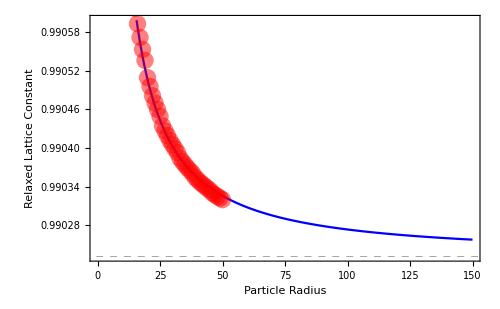

```mathematica
With[{min=limitingLatticeConstant/.newLatticeConstantModelFit},
Show[Plot[newLatticeConstantModel/.newLatticeConstantModelFit,{radius,5,150},Frame->True,FrameLabel->{"Particle Radius","Relaxed Lattice Constant"},LabelStyle->Directive[Black,16],PlotRangePadding->{Automatic,Scaled[.05]},PlotRange->{min,Automatic},ImageSize->500,PlotStyle->Blue,GridLinesStyle->Directive[Gray, Dashed],GridLines->{None,{min}}],ListPlot[latticeConstantData,PlotStyle->Directive[PointSize[0.025],Opacity[0.5],Red]]
]]
```

The limiting constant appears to be ~1% smaller than unity

The differences are small, but we might as well define a rule to return this as a function of radius

```mathematica
equilibriumLatticeConstant[radius_]=newLatticeConstantModel/.newLatticeConstantModelFit
```

0.990231+0.00918785/radius^1.17073

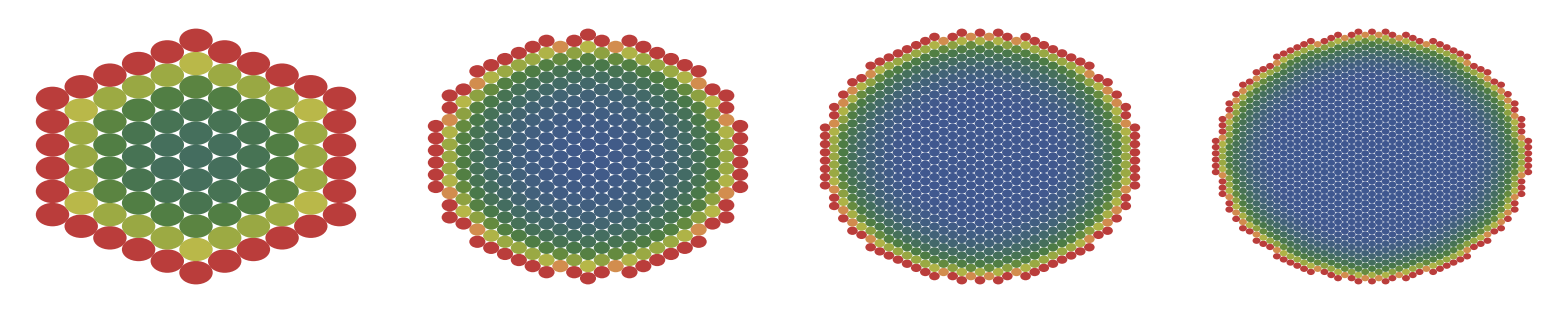

```mathematica
{ljRelaxedEnergyMinimum,ljRelaxedEnergyMaximum}=MinMax[lennardJonesEnergies[hexagonalParticle[50,hexagonalLatticePoints equilibriumLatticeConstant[50]]]];
Multicolumn[Graphics[particleGraphic[{ljRelaxedEnergyMinimum,ljRelaxedEnergyMaximum}][hexagonalParticle[#,hexagonalLatticePoints equilibriumLatticeConstant[#]]]]&/@{5,10,15,20},4]
```

Turns out, this has a fairly significant effect on the surface energy!

```mathematica
strainRelaxedParticles = <|# -> hexagonalParticle[#,equilibriumLatticeConstant[#]hexagonalLatticePoints]&/@Range[5,50] |>;
```

```mathematica
totalEnergyModelFitStrainRelaxed=With[{totalEnergies=(aggregatedLennardJonesEnergies/@strainRelaxedParticles)[[All,"Total Energy"]]},
FindFit[KeyValueMap[List,totalEnergies],totalEnergyModel,{bulkEnergy,γ},radius]
]
```

{bulkEnergy→-3.97194,γ→1.24918}

### Full Relaxation

Since the uniform strain had such an effect on surface energy, it stands to reason whether our approximation for uniform strain is valid

In theory, there’s nothing stopping the particles in relaxing non-uniformly

and in-fact there's a very rich literature of so-called “surface-reconstruction” phenomena

One approach would be to minimize the total energy with respect to all the particles’ degrees of freedom

Let’s start small, by considering a particle with radius 3

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{2.44736,{-78.7961,{x_1→-0.857173,y_1→-2.48238,x_2→-1.72122,y_2→-1.98353,x_3→0.857172,y_3→-2.48238,x_4→-6.19149×10^-7,y_4→-1.98239,x_5→-0.857991,y_5→-1.48608,x_6→-1.7168,y_6→-0.991197,x_7→-2.57839,y_7→-0.498859,x_8→1.72122,y_8→-1.98353,x_9→0.857989,y_9→-1.48608,x_10→-6.03021×10^-7,y_10→-0.990396,x_11→-0.857708,y_11→-0.495198,x_12→-1.71598,y_12→-5.8384×10^-7,x_13→-2.57839,y_13→0.498858,x_14→1.7168,y_14→-0.991197,x_15→0.857707,y_15→-0.495198,x_16→-5.93711×10^-7,y_16→-6.17661×10^-7,x_17→-0.857708,y_17→0.495197,x_18→-1.7168,y_18→0.991196,x_19→2.57839,y_19→-0.498859,x_20→1.71598,y_20→-6.27037×10^-7,x_21→0.857707,y_21→0.495197,x_22→-6.24638×10^-7,y_22→0.990395,x_23→-0.857991,y_23→1.48608,x_24→-1.72122,y_24→1.98352,x_25→2.57839,y_25→0.498858,x_26→1.7168,y_26→0.991196,x_27→0.857989,y_27→1.48608,x_28→-5.80652×10^-7,y_28→1.98239,x_29→-0.857173,y_29→2.48238,x_30→1.72122,y_30→1.98352,x_31→0.857172,y_31→2.48238}}}

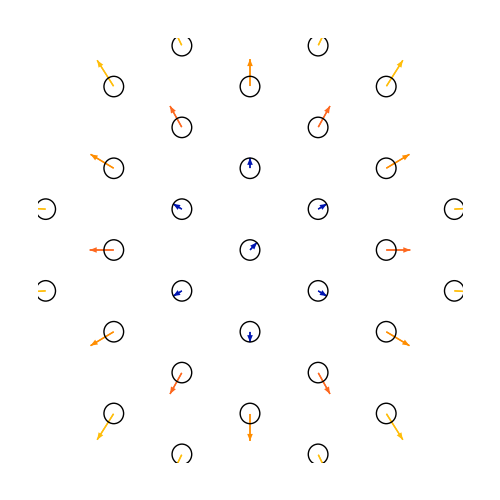

```mathematica
equilibriumPositions[3]=hexagonalParticle[3];
variables[3] = Flatten[Table[{Subscript[x,i],Subscript[y,i]},{i,Length[equilibriumPositions[3]]}]];
initialGuess[3] = Thread[{variables[3], Flatten[equilibriumPositions[3]]}];
AbsoluteTiming[{minval[3],minpos[3]}=FindMinimum[totalLennardJonesEnergyVector[variables[3]],initialGuess[3]]]

With[{us=equilibriumPositions[3]-Partition[variables[3]/.minpos[3],2]},
ListVectorPlot[Thread[{equilibriumPositions[3],us}],VectorMarkers->Placed["Arrow","Start"],VectorPoints->equilibriumPositions[3],Epilog->{Circle[#,1/8]&/@equilibriumPositions[3]},VectorScaling->Automatic,PlotRangePadding->Scaled[.1],Frame->False,ImageSize->500]
]
```

The result seems correct, but notice we get a numerical accuracy warning

We can trying helping Mathematica a bit, by providing the Gradient used in the Quasi-Newton algorithm symbolically

```mathematica
symbolicGradient[variables__]:=symbolicGradient[variables]=Module[{energy,listVars={variables}},
energy[variables]=Total[lennardJonesEnergies[Partition[listVars,2]]]/.Abs[Abs[a_]^2+Abs[b_]^2]^c_:>(a^2+b^2)^c;
Grad[energy[variables],listVars]
]
```

```mathematica
AbsoluteTiming[{minval[3],minpos[3]}=FindMinimum[totalLennardJonesEnergyVector[variables[3]],initialGuess[3],Gradient->symbolicGradient@@variables[3]];]
```

{0.165246,Null}

Not only does this not complain anymore, it is also much faster

However, when the search space is even larger, it still fails

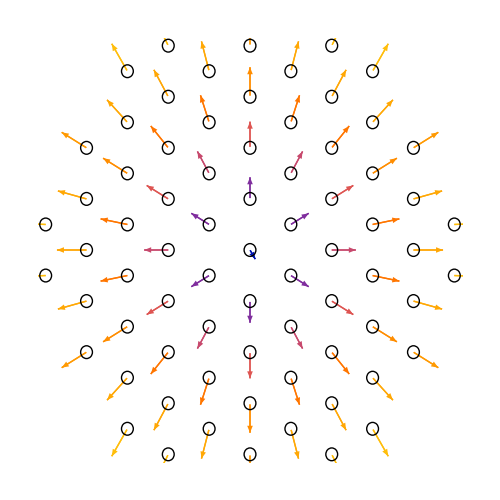

```mathematica
equilibriumPositions[4.5]=hexagonalParticle[4.5];
variables[4.5] = Flatten[Table[{Subscript[x,i],Subscript[y,i]},{i,Length[equilibriumPositions[4.5]]}]];
initialGuess[4.5] = Thread[{variables[4.5], Flatten[equilibriumPositions[4.5]]}];
AbsoluteTiming[{minval[4.5],minpos[4.5]}=FindMinimum[totalLennardJonesEnergyVector[variables[4.5]],initialGuess[4.5],Gradient->symbolicGradient@@variables[4.5]]];

With[{us=equilibriumPositions[4.5]-Partition[variables[4.5]/.minpos[4.5],2]},
ListVectorPlot[Thread[{equilibriumPositions[4.5],us}],VectorMarkers->Placed["Arrow","Start"],VectorPoints->equilibriumPositions[4.5],Epilog->{Circle[#,1/8]&/@equilibriumPositions[4.5]},VectorScaling->Automatic,PlotRangePadding->Scaled[.1],Frame->False,ImageSize->500]
]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

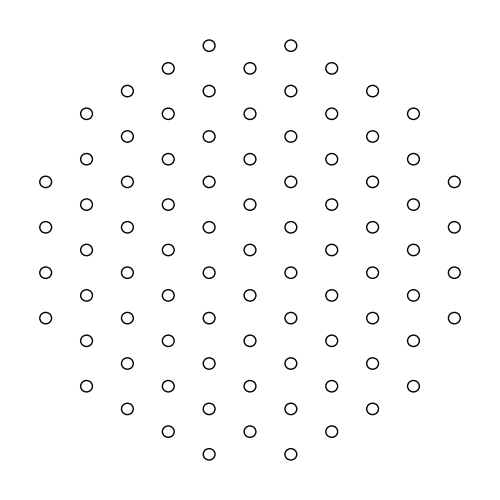

```mathematica
equilibriumPositions[5]=hexagonalParticle[5];
variables[5] = Flatten[Table[{Subscript[x,i],Subscript[y,i]},{i,Length[equilibriumPositions[5]]}]];
initialGuess[5] = Thread[{variables[5], Flatten[equilibriumPositions[5]]}];
{minval[5],minpos[5]}=FindMinimum[totalLennardJonesEnergyVector[variables[5]],initialGuess[4],Gradient->symbolicGradient@@variables[5]];

With[{us=equilibriumPositions[5]-Partition[variables[5]/.minpos[5],2]},
ListVectorPlot[Thread[{equilibriumPositions[5],us}],VectorMarkers->Placed["Arrow","Start"],VectorPoints->equilibriumPositions[5],Epilog->{Circle[#,1/8]&/@equilibriumPositions[5]},VectorScaling->Automatic,PlotRangePadding->Scaled[.1],Frame->False,ImageSize->500]
]
```

We could use a Gradient-free method like Interior Point

However, this is much too slow to be practical

```mathematica
{minval[5],minpos[5]}=FindMinimum[totalLennardJonesEnergyVector[variables[5]],initialGuess[5],Method->"InteriorPoint",MaxIterations->100];

With[{us=equilibriumPositions[5]-Partition[variables[5]/.minpos[5],2]},
ListVectorPlot[Thread[{equilibriumPositions[5],us}],VectorMarkers->Placed["Arrow","Start"],VectorPoints->equilibriumPositions[5],Epilog->{Circle[#,1/8]&/@equilibriumPositions[5]},VectorScaling->Automatic,PlotRangePadding->Scaled[.1],Frame->False,ImageSize->500]
]
```

$Aborted

### Shell Relaxation

Looking at the arrows above, it’s clear that the displacement is mostly on the outermost atoms

Perhaps we can combine the two methods

I.e. uniform strain in the core of the particle, with full relaxation on the outer shell

```mathematica
carveInnerShell[radiusOuter_,dr_:2]:=With[{
uniformStrained=hexagonalParticle[radiusOuter,equilibriumLatticeConstant[radiusOuter] hexagonalLatticePoints],
radiusInner=radiusOuter-dr},
Values[KeySort[GroupBy[uniformStrained,Norm[#]>radiusInner&]]]
]
```

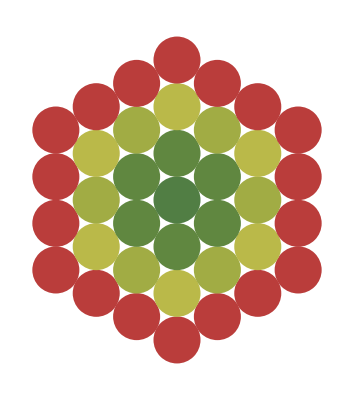
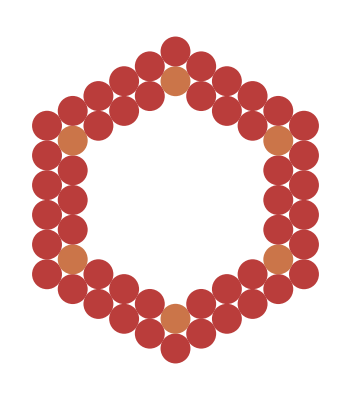

```mathematica
Graphics@*particleGraphic[{ljRelaxedEnergyMinimum,ljRelaxedEnergyMaximum}]/@carveInnerShell[5]
```

```mathematica
semiSymbolicGradient[innerPositions_][variables__]:=semiSymbolicGradient[innerPositions][variables]=Module[{energy,listVars={variables}},
energy[variables]=Total[lennardJonesEnergies[Join[innerPositions,Partition[listVars,2]]]]/.Abs[Abs[a_]^2+Abs[b_]^2]^c_:>(a^2+b^2)^c;
Grad[energy[variables],listVars]
]
```

```mathematica
Monitor[
Do[
With[{dr=2},
{innerPositions[radius],outerPositions[radius]}=carveInnerShell[radius,dr];
outerVariables[radius] = Flatten[Table[{Subscript[x,i],Subscript[y,i]},{i,Length[outerPositions[radius]]}]];
initialGuessOuter[radius] = Thread[{outerVariables[radius], Flatten[outerPositions[radius]]}];
{minvalOuter[radius],minposOuter[radius]}=FindMinimum[totalLennardJonesEnergyVector[Join[Flatten[innerPositions[radius]],outerVariables[radius]]],initialGuessOuter[radius],Gradient->semiSymbolicGradient[innerPositions[radius]]@@outerVariables[radius]];
minposShells[radius]=Join[innerPositions[radius],Partition[outerVariables[radius]/.minposOuter[radius],2]];
],{radius,2,9}],radius]
```

```mathematica
shellRelaxedParticles = <|# -> minposShells[#]&/@Range[2,9] |>;
```

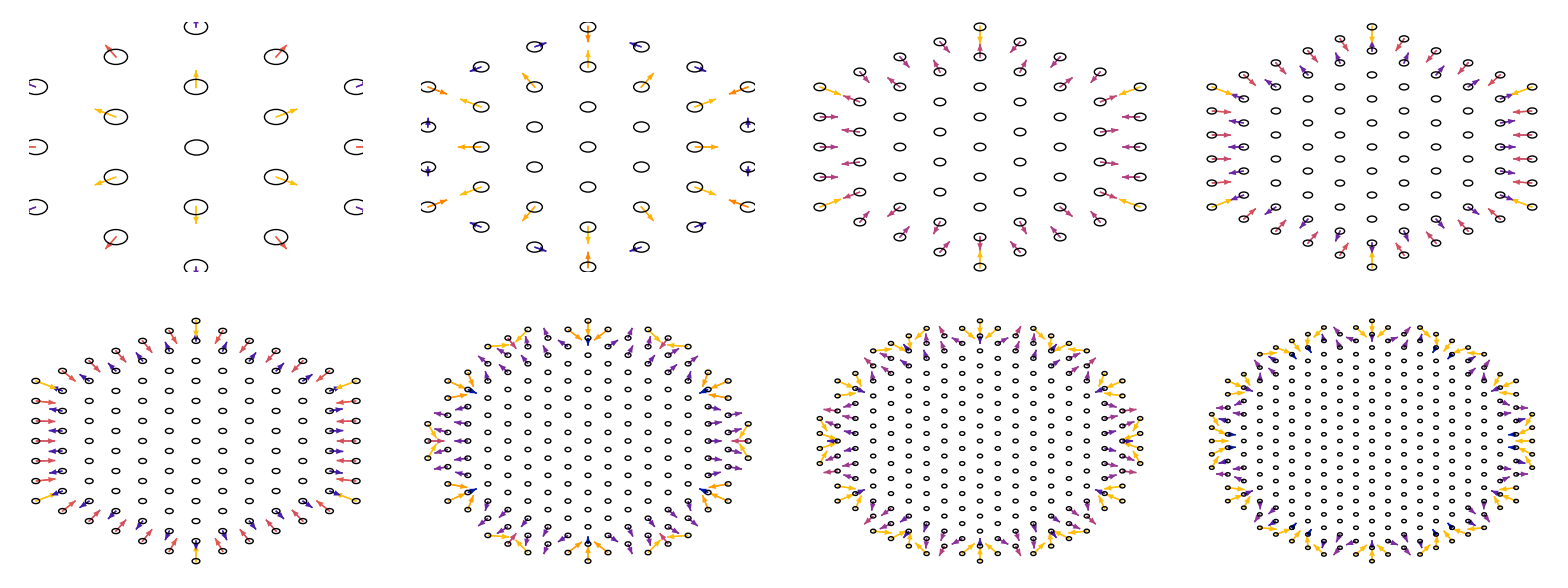

```mathematica
Multicolumn[With[{ps=Join[innerPositions[#],outerPositions[#]]},
ListVectorPlot[Thread[{ps,ps-minposShells[#]}],VectorMarkers->Placed["Arrow","Start"],VectorPoints->ps,Epilog->{Circle[#,1/8]&/@ps},VectorScaling->Automatic,PlotRangePadding->Scaled[.1],Frame->False,ImageSize->200]
]&/@Range[2,9],4,Appearance->"Horizontal"]
```

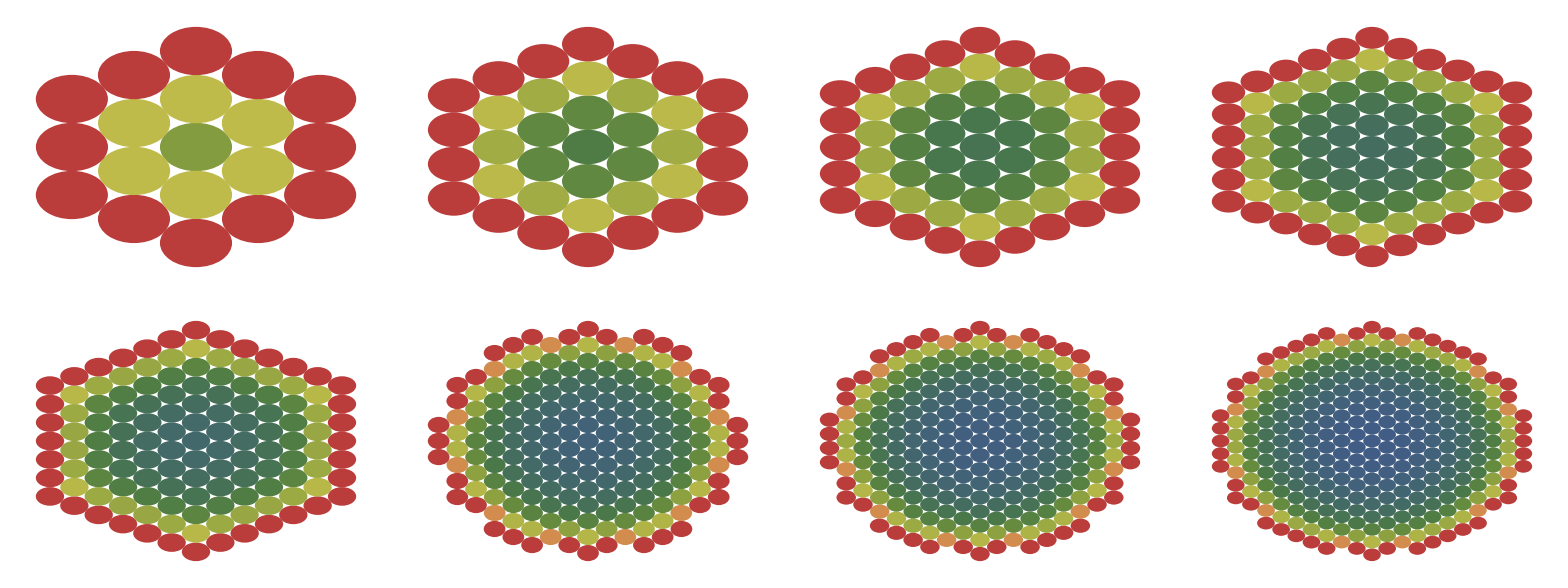

```mathematica
Multicolumn[Graphics@*particleGraphic[{ljRelaxedEnergyMinimum,ljRelaxedEnergyMaximum}]/@Values[shellRelaxedParticles],4,Appearance->"Horizontal"]
```

```mathematica
totalEnergyModelFitStrainRelaxed=With[{totalEnergies=(aggregatedLennardJonesEnergies/@shellRelaxedParticles)[[All,"Total Energy"]]},
FindFit[KeyValueMap[List,totalEnergies],totalEnergyModel,{bulkEnergy,γ},radius]
]
```

{bulkEnergy→-3.95839,γ→1.18712}

As expected, the surface reduces even further

Note however we didn’t use too large particles for this

## Orientational Dependence

We’ve seen in L08 that preferred directions in crystals result in anisotropic physical properties.

Similarly, we expect the surface energy density to be anisotropic

Some orientations will be close-packed and others will have jogs.

In ionic crystals—like NaCl which forms cubic particles—the orientation dependence will be even greater

For a Lennard Jones solid we shouldn’t expect too much anisotropy

The potential is centro-symmetric

Fairly short-ranged

and the hexagonally-closed packed structure is as “isotropic” as crystals can get

Nonetheless, we will recover some anisotropy in the surface energy density

First, let’s get a sense of the anisotropy graphically by “cleaving” our round particle at a particular orientation

We’ll use the uniformly-strained lattice

```mathematica
cleaveParticle[radius_][rotation_]:=With[{round=hexagonalParticle[radius, equilibriumLatticeConstant[radius]hexagonalLatticePoints]},
KeySort[GroupBy[round,Chop[ #.AngleVector[rotation]]<  0&]]//Values
]
```

```mathematica
Manipulate[
Graphics[{
particleGraphic[{ljRelaxedEnergyMinimum,ljRelaxedEnergyMaximum}]/@cleaveParticle[radius][θ],
{Black,Thick,Dashed,InfiniteLine[{0,0},AngleVector[θ-π/2]]}
},PlotRange->radius{{-1.05,1.05},{-1.05,1.05}}],
{{radius,10,"Particle Radius"},5,15,5/2},{{θ,π/4,"Surface Orientation"},0,2π},Paneled->False]
```

We wish to isolate the orientation-dependent part of the surface energy, by subtracting the bulk energy and surface energy contributions from the round part of the surface

To do so we will compute the average LJ energy for the two cleaved halves and fit it to half the energy model we used earlier, plus a

```mathematica
cleavedParticleEnergyModel=(bulkEnergy (Pi radius^2) + γ (2 Pi radius))/2+2 σ radius+2ρ;
```

```mathematica
cleavedParticles = Association@Table[θ->Association@Table[radius->cleaveParticle[radius][θ],{radius,Range[5,50,5]}],{θ,0,2 Pi,Pi/36}];
```

```mathematica
Clear[anisotropicFit]
anisotropicFit[θ_]:=anisotropicFit[θ]=Block[{data,fit},
data=Table[{r,Mean[(aggregatedLennardJonesEnergies/@cleavedParticles[θ][r])[[All,"Total Energy"]]]},{r,5,50,5}];
fit=FindFit[data,cleavedParticleEnergyModel,{σ,ρ,bulkEnergy,γ},radius];
<|"θ"->θ,"σ"-> σ/.fit,"ρ"-> ρ/.fit|>
]
```

```mathematica
ListPolarPlot[(anisotropicFit/@Range[0,2π,π/36])[[All,{"θ","σ"}]],PlotStyle->Directive[PointSize[0.025],Opacity[0.5],Red], PolarGridLines->Automatic, PolarAxes->Automatic,PolarTicks->Automatic,PolarAxesOrigin->{0,2.5},PlotRange->3.25{{-1,1},{-1,1}},ImageSize->500,BaseStyle->Directive[Black,16]]
```

-Graphics-